# Report Project 2 - Encryption

```mathematica
IX1500 - Course
Date: 2018-10-04
```

Josef Federspiel joseffe@kth.se
Linus Bein Fahlander, linusfa@kth.se

## Code Segment

```mathematica
(*Solution to task 1*)
```

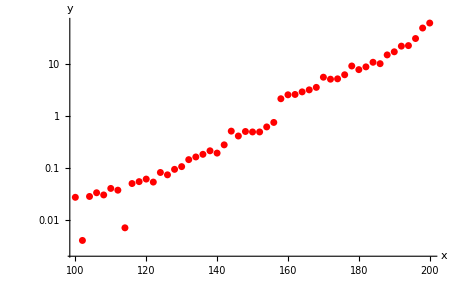
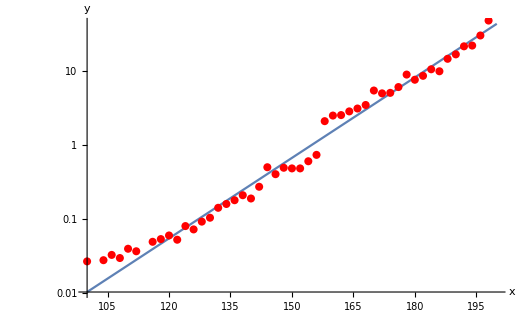
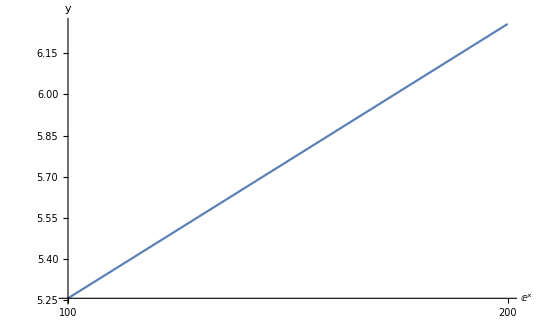
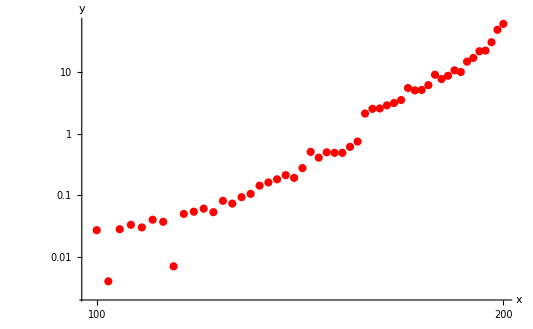
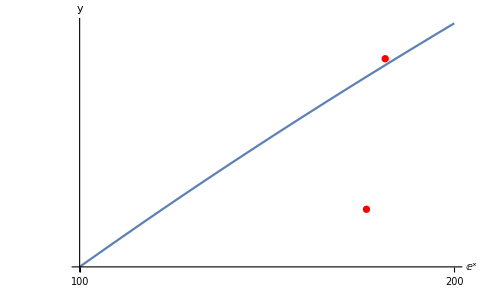
```mathematica
n=126456119090476383371855906671054993650778797793018127;
e=7937;
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
(*The method we use to crack the encryption for task one, and also the method we use to crack the standard RSA cipher*)
crackRSA[cipher_, n_, e_]:=Module[{divs,p,q,phi,d,decryptF, extractF,decryptCipher,decryptAscii},
divs=Divisors[n];
p=divs[[2]];
q=divs[[3]];
phi=(p-1)(q-1);
d=PowerMod[e,-1,phi];
decryptF[msg_]:=Return[PowerMod[msg,d,n]];
decryptCipher=decryptF/@cipher;
extractF[msg_]:=Module[{m=msg,localStore={}},
While[m≠0,AppendTo[localStore,Mod[m, 256]];m=Quotient[m, 256]];
Return[localStore];
m
];
decryptAscii=extractF/@decryptCipher;
Return[FromCharacterCode[Flatten[decryptAscii]]];
];
crackRSA[cipher, n, e]
"Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.  "
(*The function encrypts the mesage in task 2 and then cracks it. Messuring the time it takes to crack the cipher*)
loopCall[size_,cipher_]:=Module[{n,e,p,q,phi,B,stringPat,range,pattedMsg,codePats,codedMsg,encryptF,encryptedMsg,crackedMsg,startTime,endTime},
stringPat[s_,n_]:=StringCases[s,Repeated[_,n]];
range[msg_]:=Range[StringLength[msg]]-1;
codePats[pat_]:=ToCharacterCode[pat].(B^range[pat]);
encryptF[msg_]:=Return[PowerMod[msg,e,n]];
p=NextPrime[RandomInteger[{2^(IntegerPart[size/2] - 1),(2^(IntegerPart[size/2]))-1}]];
q=NextPrime[RandomInteger[{2^(IntegerPart[size/2] - 1),(2^(IntegerPart[size/2]))-1}]];
n=p q;
phi=(p-1)(q-1);
While[GCD[e=RandomInteger[{10^3,10^4}],phi]≠1];
B=256;
pattedMsg=stringPat[cipher,Divisors[StringLength[cipher]][[2]]];
codedMsg=codePats/@pattedMsg;
encryptedMsg=encryptF/@codedMsg;
startTime=AbsoluteTime[];
crackedMsg=crackRSA[encryptedMsg,n,e];
endTime=AbsoluteTime[];
Print[crackedMsg];
Return[endTime-startTime];
];
loopCall[100,"ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL."]
"ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL."
0.0259305`5.865355884547908
executeTimes={};
For[i=100,i<=200,i=i+2,AppendTo[executeTimes,loopCall[i,"ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL."]]];
executeTimes
{0.0269285`5.881757156047249,0.0039903`5.052550541675643,0.0279509`5.897940789930966,0.0329384`5.969247492760561,0.0298947`5.927139193031761,0.0398925`6.052436247208253,0.036902`6.018594898013452,0.00698`5.295400416119134,0.0495336`6.146444886253695,0.0538757`6.182937919433434,0.0603083`6.231922080033166,0.0528346`6.174463417312722,0.0807819`6.358859057108494,0.0728056`6.3137097787920196,0.0927804`6.41900123403718,0.1047202`6.471575456477301,0.142592`6.605640153981551,0.1605716`6.6572137283741,0.180516`6.708060695049298,0.2109444`6.775712994029796,0.1904908`6.731418999199388,0.2743669`6.8898767098075275,0.5036691`7.153690301290092,0.4059124`7.05997731204489,0.4956815`7.146747703811564,0.4857289`7.13793893748195,0.4856998`7.137912918136573,0.6068073`7.234595790282135,0.7399925`7.320772311571379,2.1118361`7.776205202988575,2.5138692`7.851887670506988,2.5517896`7.858389856599198,2.8613322`7.908113275716319,3.1293242`7.946995552160663,3.4920673`7.994627598442729,5.4766435`8.190059465112755,5.0147581`8.151794982025102,5.0949533`8.158685201142585,6.1008388`8.23693454345224,8.9954079`8.405565854863221,7.6593007`8.335734113520887,8.653701`8.388746879009313,10.6072475`8.477147695903811,9.9655062`8.450044357173045,14.6920422`8.618627160596457,16.8642829`8.67851287242207,21.6588705`8.78718079812102,22.1799961`8.797506458945335,30.3436512`8.933612831008201,48.278267`9.135296665736417,60.211355`9.231223394202562}
xValues=Range[100,200,2];
data=Transpose[{xValues,executeTimes}];
dataplot=ListLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
(*The attempt to plot the data in a exponential function *)
-Graphics-
exponentialData=Transpose[{xValues,Log[executeTimes]}];
expSolution=FindFit[exponentialData, a x+b,{a,b},x]
{a->0.0834290100411870576`5.794795473946688,b->-12.9099610492764056305`5.794795473946688}
yExp[x_]=ⅇ^(a x+b)/.expSolution
ⅇ^(-12.9099610492764056305`5.794795473946688+0.0834290100411870576`5.794795473946688 x)
modelplotExp=LogPlot[yExp[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotExp,dataplot]
-Graphics-
logarithmicData=Transpose[{Log[xValues],executeTimes}];
logSolution=FindFit[logarithmicData,a lnx+b,{a,b},lnx]
yLog[x_]=a Log[x]+b/.logSolution
modelplotLog=LogLinearPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotLog,dataplot]
{a->36.7951423876366268323`5.052550541675643,b->-177.6693874665786170068`5.052550541675643}
-177.6693874665786170068`5.052550541675643+36.7951423876366268323`5.052550541675643 Log[x]
(*The attempt to plot the data in a logarithmic function *)
-Graphics-
(*The attempt to plot the data in a power function *)
dataplotPow=ListLogLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
-Graphics-
dataPow=Transpose[{Log[xValues],Log[executeTimes]}];
solutionPow=FindFit[dataPow,a lnx+b,{a,b},lnx]
yPow[x_]=ⅇ^b x^a/.solutionPow
modelplotPow=LogLogPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotPow,dataplotPow]
{a->12.0789675052916414331`5.794795473946688,b->-60.6777426806137483061`5.794795473946688}
4.446222370843610854597587417367`4.011766058054609*^-27 x^(12.0789675052916414331`5.794795473946688)
-Graphics-
(*Creating a table to visualize the time it takes to crack ciphers for large public keys*)
L1 = 1024
L2 =2048
L3 = 4096

Grid[{{"Bits n","Time"},
 {L1//N, ⅇ^(-12.9099610492764056305`5.794795473946688+0.0834290100411870576`5.794795473946688 1024)//N},
  {L2//N, ⅇ^(-12.9099610492764056305`5.794795473946688+0.0834290100411870576`5.794795473946688 2048)//N}, 
  {L3//N, ⅇ^(-12.9099610492764056305`5.794795473946688+0.0834290100411870576`5.794795473946688 4096)//N}},
Frame->All, Background->{{LightBrown, None},{LightGray, None}},Alignment->Left]

1024
2048
4096
{{"Bits n", "Time"}, {1024., 3.130545749087181*^31}, {2048., 3.962460582340433*^68}, {4096., 6.348260727916298*^142}}
```

## Task 1

### Summary

#### Task

Professor Alice is sending a message to the student Bob according to the procedure in section Section.Subsection.4. You are supposed to crack the message. When translating to ASCII, you can assume the base 256.
nBob=126456119090476383371855906671054993650778797793018127;
eBob=7937;
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
The numbers is the list seems to be of the same size. Why?

#### Result

When cracked the messaged is revealed to be.   
“Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem. “

#### Discussion

The reason the numbers on the list seem to be the same size so that there is no way to determine what the contents of the cipher could be. If the numbers size were dependent on the size of the string then you could possibly find patterns in a larger text and from there crack the encryption so by padding every string and keeping them the same length you avoid this problem.

## Task 2

### Summary

#### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits
Motivate your selected mathematical model!

#### Result

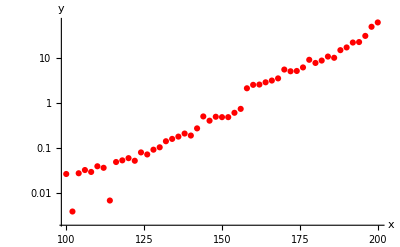
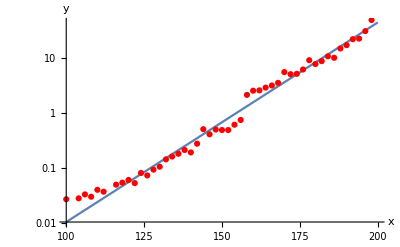
We encrypted and cracked the message. With size 100 - 200 bits on the public key n. Then plotted the data i a semi log plot with the x axis linear and a the y axis logarithmic resulting in the following graphs.  
-Graphics-
-Graphics-
These graphs give us a model to calculate how long it would take to crack a message  with a public key with a length of n bits.
Model : ⅇ^(-12.91+0.083429 x)

"Bits n" | "Time"
1024. | 3.13055×10^31
2048. | 3.96246×10^68
4096. | 6.34826×10^142

#### Discussion

When selecting out mathematical method we plotted our data in a graph and saw how the time it took to crack the cipher grew rapidly and therefore we could see that i was not  a linear function.  We the plotted the our data in a log(y) - lin(x) plot, since the data fit a straight line  knew that the model was exponential. We then plotted our data in a lin(y)-log(x) plot to see if it was logarithmic function and we could conclude that it was not. We then plotted our data in a log(y)-log(x) plot and saw that it was not a power function. Leaving us with the conclusion that it was exponential.